```mathematica
Quit
```

```mathematica
p = 0; q = -1; f[x_]:= -2  Exp[-2 x]; n = 200;a = 1; b = 2; h =(b - a)/n;Subscript[x, 0]=a; Subscript[x, n]=b;
getCoefs[expr_]:= Table[Coefficient[expr, Subscript[y, i],1], {i, 0, n}];
(*Формируем правую часть линейной системы*)
```

```mathematica
mainRight = Table[Subscript[x, i]= Subscript[x, i-1]+h; f[Subscript[x, i]], {i, 1, n-1}];
boundaryRight = {0, 1};
F = Join[{boundaryRight[[1]]}, mainRight, {boundaryRight[[2]]}];
(*Получаем основные уравнения+краевые условия*)
```

```mathematica
mainEq=Table[(Subscript[y, i-1]- 2 Subscript[y, i]+Subscript[y, i+1])/h^2+ p (Subscript[y, i+1] - Subscript[y, i])/h + q Subscript[y, i], {i, 1, n-1}];
boundary= {Subscript[y, 0]+(Subscript[y, 1]-Subscript[y, 0])/h, (Subscript[y, n]-Subscript[y, n-1])/h};
allEq =Join[{boundary[[1]]},mainEq,  {boundary[[2]]}];
totalMatrix = (getCoefs /@ allEq);
(*Решаем линейную систему методом прогонки*)
```

```mathematica
A = Table[If[i==1, 0,totalMatrix[[i, i-1]]], {i, 1, n+1}];
B = Table[totalMatrix[[i, i]], {i, 1,n+1}];
G= Table[If[i==n+1,0,totalMatrix[[i, i+1]]], {i, 1, n+1}];
Subscript[α, 1]= -G[[1]]/B[[1]];
Subscript[β, 1]= F[[1]]/B[[1]];
Do[Subscript[α, i]= (-G[[i]])/(A[[i]] Subscript[α, i-1]+ B[[i]]); Subscript[β, i]=(F[[i]]- A[[i]] Subscript[β, i-1])/(A[[i]] Subscript[α, i-1]+ B[[i]]), {i, 2, n+1}]
Subscript[y, n]=(F[[n+1]] -  A[[n+1]] Subscript[β, n+1])/(B[[n+1]] + A[[n+1]] Subscript[α, n+1]);
Do[Subscript[y, i]= Subscript[α, i+1] Subscript[y, i+1]+ Subscript[β, i+1], {i, n-1, 0, -1}];
val =Table[Subscript[y, i], {i, 0, n}] //N;
```

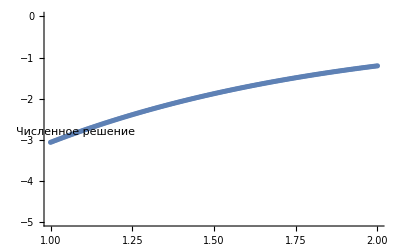

```mathematica
xs = Table[Subscript[x, i], {i, 0, n}];
points=Transpose[{xs, val}];
gr1 =ListPlot[points,PlotLabels->Placed[{"Численное решение"}, Bottom]];
Show[gr1, PlotRange-> {{1, 2}, {-5, 0}}]
```

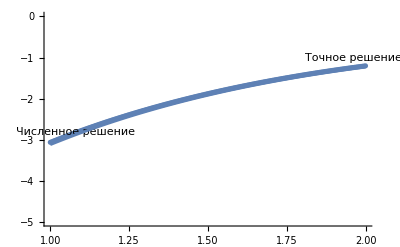

```mathematica
realSolution =DSolve[{y''[x] + p y'[x] + q y[x] == f[x], y[a]+y'[a] == 0, y'[b]==1}, y[x], x];
gr2 =Plot[realSolution[[1, 1, 2]], {x, a, b},PlotLabels->Placed[{"Точное решение"}, Above]];
Show[{gr1,gr2}, PlotRange-> {{1, 2}, {-5, 0}}]
```